```mathematica
Clear["Global`*"]
(*Data import*)
SetDirectory[NotebookDirectory[]];
dataI=Import["CSV\\time_series_covid_19_confirmed.csv","Data"];
dataD=Import["CSV\\time_series_covid_19_deaths.csv","Data"];
dataR=Import["CSV\\time_series_covid_19_recovered.csv","Data"];
dataPop=Import["CSV\\population.csv ","Data"];
(*Returns a population of a country.country is a string,for←-example," China "*)
population[country_]:=Module[{pos}, 
pos=Position[dataPop[[All,1]],country][[1,1]]; 
dataPop[[pos,2]] ]

(*Small tricks for ticks*)
 dates=dataI[[1,5;;]];
 datesTicks=Transpose[{Range[Length[dates]],dates}];
(*Returns a List of cases according to the dates.*)
CasesPerCountry[data_,country_]:=Module[
{countryData,pos}, countryData=data[[2;; ,2]];
pos=Flatten@Position[countryData,country];
Plus@@data[[pos+1]][[All,5;;]]
 ]
 IList=CasesPerCountry[dataI,"Belarus"]//N
 RList=CasesPerCountry[dataR,"Belarus"]//N
DList= CasesPerCountry[dataD,"Belarus"]//N
Nt=population["Belarus"];
Time=83-38+5;
syst = {
s'[t]==-beta*s[t]*i[t],
i'[t]==beta*s[t]*i[t]-mu*i[t],
r'[t]==mu*i[t],
r[0]==0,
i[0]==i0,
s[0]==1-r[0]-i[0]
};
solS=ParametricNDSolveValue[syst, s, {t,0,Time},{beta, mu, i0}];
solI=ParametricNDSolveValue[syst, i, {t,0,Time},{beta, mu, i0}];
solR=ParametricNDSolveValue[syst, r, {t,0,Time},{beta, mu, i0}];
IListT=Table[{i,IList[[i+38]]},{i,0,Length[IList]-38}];
RListT=Table[{i,RList[[i+38]]},{i,0,Length[RList]-38}];

ifit=Quiet@FindFit[IListT,Nt*solI[beta, mu,i0][t],{{beta,0.2}, {mu,0.0174},{i0,1/Nt}},t,Method->{NMinimize,Method->{"DifferentialEvolution"}}]
rfit=Quiet@FindFit[RListT,Nt*solR[beta, mu,i0][t],{{beta,0.2}, {mu,0.0174},{i0,1/Nt}},t,Method->{NMinimize,Method->{"DifferentialEvolution"}}]
sfit=Quiet@FindFit[IListT,Nt*(1-solS[beta, mu,i0][t]),{{beta,0.19}, {mu,0.0174},{i0,1/Nt}},t,Method->{NMinimize,Method->{"DifferentialEvolution"}}]
plotCases[data_,country_,legend_]:= ListPlot[Table[ CasesPerCountry[data[[k]],country],{k,1,Length[data]}],FrameTicks->{datesTicks[[1;; ;;14]],Automatic}, FrameLabel->{"Date","People"},PlotLabel->country, PlotTheme->"Scientific",PlotLegends->legend,PlotRange->All,GridLines->Automatic]
(*Call of plotCases[]*)
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,6.,6.,6.,6.,6.,6.,9.,9.,12.,27.,27.,27.,36.,36.,51.,51.,69.,76.,76.,81.,81.,86.,86.,94.,94.,94.,152.,152.,163.,304.,351.,440.,562.,700.,861.,1066.,1486.,1981.,2226.,2578.,2919.,3281.,3728.,4204.,4779.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,3.,3.,3.,3.,3.,3.,3.,3.,5.,5.,5.,15.,15.,15.,22.,29.,29.,32.,32.,32.,32.,47.,53.,53.,53.,53.,52.,53.,54.,77.,139.,169.,172.,203.,203.,203.,203.,203.,342.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,2.,4.,4.,5.,8.,13.,13.,13.,16.,19.,23.,26.,29.,33.,36.,40.,42.}

{beta→0.191945,mu→0.0174,i0→9.31927×10^-8}

{beta→-1.29421,mu→-0.63244,i0→-6.13395×10^-6}

{beta→0.19,mu→0.0193495,i0→1.05446×10^-7}

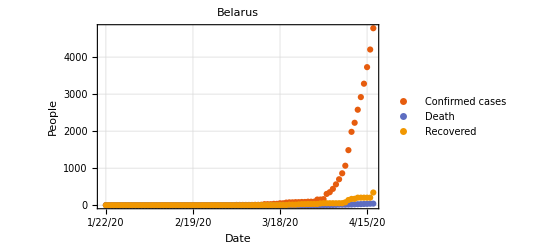

InterpolatingFunction[{{0., 50.}}, <>][t]

9483499 InterpolatingFunction[{{0., 50.}}, <>][p]

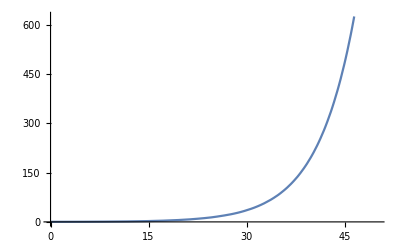

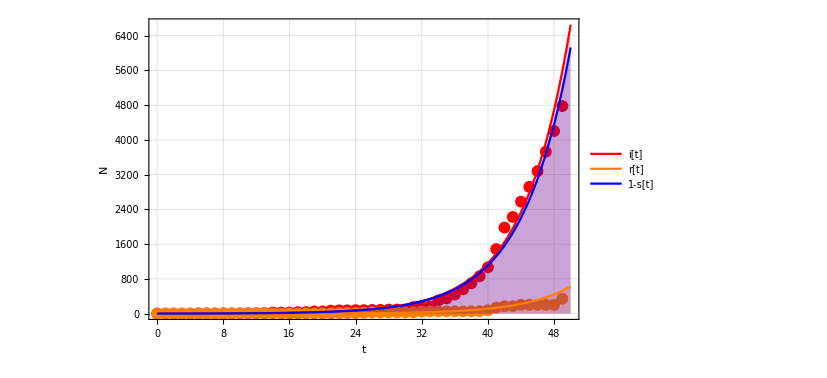

```mathematica
plotCases[{dataI,dataD,dataR},"Belarus",{"Confirmed cases", "Death","Recovered"}]
solI[ifit[[1,2]], ifit[[2,2]],1/Nt][t]
dSolI=Nt*D[solI[ifit[[1,2]], ifit[[2,2]],1/Nt][p],p]
Plot[dSolI/.{p->t},{t,0,50}]

Show[ListPlot[{IListT,RListT},PlotRange->All,PlotStyle->{Red,Orange}],
Plot[{
Nt*solI[ifit[[1,2]], ifit[[2,2]],1/Nt][t],
Nt*solR[sfit[[1,2]], sfit[[2,2]],1/Nt][t],
Nt*(1-solS[sfit[[1,2]], sfit[[2,2]],1/Nt][t])
},{t,0,50},PlotRange->All,PlotLegends->Placed[{
Style["i[t]",16,Black,FontFamily->"Cambria"],
Style["r[t]",16,Black,FontFamily->"Cambria"],
Style["1-s[t]",16,Black,FontFamily->"Cambria"]},Right],PlotStyle->{Red,Orange,Blue},Filling->Bottom],
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",16,Black,FontFamily->"Cambria"],
Style["N",16,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,ImageSize->612]
```

```mathematica
(*Task 1. SIR*)
(*ssol=ParametricNDSolveValue[syst, {s[t],i[t],r[t]}, {t,0,100},{beta, mu, i0}];*)
(*ListPlot[Table[{lt,Integrate[solI[beta, mu,i0],{t,0,lt}]},{lt,0,100,1}]]*)
(*ssol[beta, mu,i0][[1]],ssol[beta, mu,i0][[2]],ssol[beta, mu,i0][[3]]*)
Manipulate[
Row[{Show[Plot[{
Nt*solS[beta, mu,i0][t],
Nt*solI[beta, mu,i0][t],
Nt*solR[beta, mu,i0][t]},

{t,0,Time},
PlotStyle->{Blue, Red,Orange},
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t, days",16,Black,FontFamily->"Cambria"],
Style["s[t],i[t],r[t], N",16,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->Automatic,PlotLegends->Placed[{
Style["s[t]",16,Black,FontFamily->"Cambria"],
Style["i[t]",16,Black,FontFamily->"Cambria"],
Style["r[t]",16,Black,FontFamily->"Cambria"]},Right],ImageSize->612]
]
(*,
Show[Plot[{
Nt*solI[beta, mu,i0][t],
Nt*solR[beta, mu,i0][t],
Nt*(1-solS[beta, mu,i0][t])},

{t,0,Time},
PlotStyle->{Red,Orange},
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",16,Black,FontFamily->"Cambria"],
Style["i[t],r[t]",16,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,PlotLegends->Placed[{
Style["i[t]",16,Black,FontFamily->"Cambria"],
Style["r[t]",16,Black,FontFamily->"Cambria"]},Right],ImageSize->324]
]*)}],
{{beta, 0.191945},0,1}, 
{{mu,0.0174},0,1}, 
{{i0, 1.0544631258989958*^-7}, 0,0.5}]
Manipulate[
Row[{
Column[{
Show[ParametricPlot[{solS[beta, mu,i0][t],(D[solS[beta, mu,i0][p],p])/.{p->t}},{t,0,Time},AspectRatio->1/2],
FrameStyle->Directive[Black,12],Frame->True, FrameLabel->{
Style["s",12,Black,FontFamily->"Cambria"],
Style["s'",12,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,ImageSize->512
],
Show[ParametricPlot[{solI[beta, mu,i0][t],(D[solI[beta, mu,i0][p],p])/.{p->t}},{t,0,Time},AspectRatio->1/2],
FrameStyle->Directive[Black,12],Frame->True, FrameLabel->{
Style["i",12,Black,FontFamily->"Cambria"],
Style["i'",12,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,ImageSize->512
],
Show[ParametricPlot[{solR[beta, mu,i0][t],(D[solR[beta, mu,i0][p],p])/.{p->t}},{t,0,Time},AspectRatio->1/2],
FrameStyle->Directive[Black,12],Frame->True, FrameLabel->{
Style["r",12,Black,FontFamily->"Cambria"],
Style["r'",12,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,ImageSize->512
]}
]}],
{{beta, 0.191945},0,1}, 
{{mu,0.0174},0,1}, 
{{i0, 1.0544631258989958*^-7}, 0,0.5}]
```

```mathematica
(*Task 1. SEIRS*)
Clear[syst,s,p,i,r,beta,gamma,mu,k,d,t,tau];
syst = {
s'[t]==-beta*k*s[t]*i[t]+gamma*r[t],
p'[t]==beta*k*s[t]*i[t]-beta*k*s[t-tau]*i[t-tau],
i'[t]==beta*k*s[t-tau]*i[t-tau]-(mu+d)*i[t],
r'[t]==mu*i[t]-gamma*r[t], 
r[0]==0,
i[0]==i0,
p[0]==k*i[0],
s[0]==1-p[0]-i[0]
};
ssol=ParametricNDSolveValue[syst, {s[t],i[t],r[t],p[t]}, {t,0,100},{beta, mu, i0, d, gamma,k,tau}]
Manipulate[Plot[{
ssol[beta, mu, i0, d, gamma,k,tau][[1]],
ssol[beta, mu, i0, d, gamma,k,tau][[2]],
ssol[beta, mu, i0, d, gamma,k,tau][[3]],
ssol[beta, mu, i0, d, gamma,k,tau][[4]]},{t,0,100},
PlotStyle->{Blue, Red,Orange,Green},
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",20,Black,FontFamily->"Cambria"],
Style["s[t],i[t],r[t]",20,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->Automatic,PlotLegends->Placed[{
Style["s[t]",20,Black,FontFamily->"Cambria"],
Style["i[t]",20,Black,FontFamily->"Cambria"],
Style["r[t]",20,Black,FontFamily->"Cambria"],
Style["e[t]",20,Black,FontFamily->"Cambria"]},Right],ImageSize->512],
{{beta, 0.2},0,1}, 
{{mu,0.2},0,1}, 
{{gamma,2*10^-4},0,0.2},
{{d,5*10^-3},0,0.01},
{{k,6},0,10},
{{tau,5},0,10},
{{i0,  0.001}, 0, 0.01}]
```

ParametricFunction[<>]